## Объявление глобальных переменных

```mathematica
(*ClearAll["Global`*"]*)
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data1=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/61/tables/nap1.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data1//TableForm
```

N | U- | I- | 
1. | 4.96 | 982. | 7.01
2. | 4.69 | 1012. | 7.11
3. | 4.1 | 981. | 7.
4. | 3.74 | 983. | 7.01
5. | 3.37 | 968. | 6.96
6. | 2.96 | 935. | 6.84
7. | 2.5 | 901. | 6.71
8. | 2.03 | 926. | 6.8
9. | 1.57 | 972. | 6.97
10. | 1.5 | 973. | 6.97
11. | 1.26 | 986. | 7.02
12. | 0.9 | 984. | 7.01
13. | 1.55 | 975. | 6.98
14. | 2.74 | 923. | 6.79
15. | 2.28 | 891. | 6.67
16. | 2.4 | 884. | 6.65
17. | -5.91 | 989. | 7.03
18. | -5.6 | 990. | 7.04
19. | -4.88 | 1076. | 7.33
20. | -4.48 | 980. | 7.
21. | -4.03 | 990. | 7.04
22. | -3.5 | 981. | 7.
23. | -2.97 | 988. | 7.03
24. | -2.37 | 989. | 7.03
25. | -1.85 | 984. | 7.01
26. | -1.78 | 964. | 6.94
27. | -1.48 | 987. | 7.02
28. | -1.05 | 989. | 7.03
29. | -1.82 | 993. | 7.05
30. | -3.26 | 1004. | 7.09
31. | -2.68 | 986. | 7.02
32. | -2.83 | 989. | 7.03

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit1=Sort@data1⟦2;;,{2,3}⟧;
model =b-a/((x-X)^2/c^2+1);
(*mean=Mean@forFit1⟦All,2⟧;
low=SplitBy[{##,#2<mean}&@@@forFit1,Last];
low=Select[low,#⟦1,-1⟧&];
low=MaximalBy[low,Length]⟦1,All,{1,2}⟧;*)
```

```mathematica
fit=NonlinearModelFit[forFit1⟦All,{1,2}⟧,{model,30<a<250,950<b<990,0.3<c<0.5},{{a,100},{b,980},{c,0.3},{X,2.5}},x,
Weights->1/√(forFit1⟦All,2⟧/20)]
fit@"ParameterTable"
(*Plot[fit["Function"]@x, {x, -5, 5}]*)
```

FittedModel[990.-102.927/(1+4.93265 (-2.41282+x)^2)]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 102.927 | 11.6543 | 8.83169 | 1.38687×10^-9
b | 990. | 4.31862 | 229.24 | 2.20512×10^-47
c | 0.450256 | 0.0993366 | 4.53263 | 0.0000994137
X | 2.41282 | 0.0673039 | 35.8496 | 6.0599×10^-25

```mathematica
fit["BestFit"]
```

990.-103.491/(1+5.21974 (-2.41183+x)^2)

```mathematica
Minimize[990.-103.49073428481594/(1+5.2197406360046275 (-2.41182781841223+x)^2),{x}]
```

{886.509,{x→2.41183}}

```mathematica
fit["CovarianceMatrix"]
```

FittedModel::constr: The property values {CovarianceMatrix} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{4426.01,389.95,-14.5119,0.269411},{389.95,570.863,5.95899,-0.277834},{-14.5119,5.95899,0.300366,-0.00620677},{0.269411,-0.277834,-0.00620677,0.139701}}

```mathematica
MatrixForm[%356]
```

(4426.01 | 389.95 | -14.5119 | 0.269411
389.95 | 570.863 | 5.95899 | -0.277834
-14.5119 | 5.95899 | 0.300366 | -0.00620677
0.269411 | -0.277834 | -0.00620677 | 0.139701)

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 103.491 | 66.5282 | 1.55559 | 0.130652
b | 990. | 23.8927 | 41.4352 | 2.32265×10^-27
c | 0.437699 | 0.548057 | 0.798638 | 0.430993
X | 2.41183 | 0.373766 | 6.45277 | 4.63633×10^-7

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,25}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

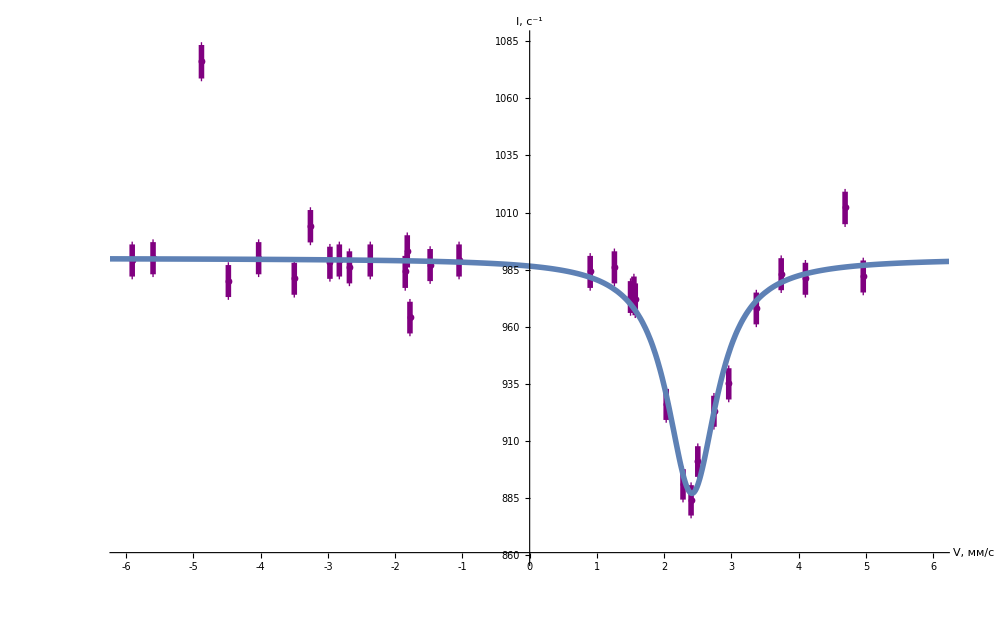

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data1⟦2;;,{2,3,4,4}⟧,
GridLines->{grids@0.25,grids@25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, мм/с","I, c^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,myTicY},
PlotRange->{{-6,6},{860,1085}}], 
Plot[fit@x,{x,-7,7},PlotRange->{{-6,6},{850,1100}}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX1=MapAt[dropLastDot@*ToString,data1,{{2;;,All}}];
forTeX1//TeXForm
```

\left(
\begin{array}{cccc}
 \text{N} & \text{U-} & \text{I-} & \text{} \\
 1 & 4.96 & 982 & 7.01 \\
 2 & 4.69 & 1012 & 7.11 \\
 3 & 4.1 & 981 & 7 \\
 4 & 3.74 & 983 & 7.01 \\
 5 & 3.37 & 968 & 6.96 \\
 6 & 2.96 & 935 & 6.84 \\
 7 & 2.5 & 901 & 6.71 \\
 8 & 2.03 & 926 & 6.8 \\
 9 & 1.57 & 972 & 6.97 \\
 10 & 1.5 & 973 & 6.97 \\
 11 & 1.26 & 986 & 7.02 \\
 12 & 0.9 & 984 & 7.01 \\
 13 & 1.55 & 975 & 6.98 \\
 14 & 2.74 & 923 & 6.79 \\
 15 & 2.28 & 891 & 6.67 \\
 16 & 2.4 & 884 & 6.65 \\
 17 & -5.91 & 989 & 7.03 \\
 18 & -5.6 & 990 & 7.04 \\
 19 & -4.88 & 1076 & 7.33 \\
 20 & -4.48 & 980 & 7 \\
 21 & -4.03 & 990 & 7.04 \\
 22 & -3.5 & 981 & 7 \\
 23 & -2.97 & 988 & 7.03 \\
 24 & -2.37 & 989 & 7.03 \\
 25 & -1.85 & 984 & 7.01 \\
 26 & -1.78 & 964 & 6.94 \\
 27 & -1.48 & 987 & 7.02 \\
 28 & -1.05 & 989 & 7.03 \\
 29 & -1.82 & 993 & 7.05 \\
 30 & -3.26 & 1004 & 7.09 \\
 31 & -2.68 & 986 & 7.02 \\
 32 & -2.83 & 989 & 7.03 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data4=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/61/tables/nap4.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data4//TableForm
```

N | U- | I- | 
1. | -5.88 | 1562. | 8.84
2. | -5.59 | 1559. | 8.83
3. | -5.26 | 1565. | 8.85
4. | -4.87 | 1550. | 8.8
5. | -4.45 | 1540. | 8.77
6. | -4.03 | 1541. | 8.78
7. | -3.48 | 1536. | 8.76
8. | -2.93 | 1520. | 8.72
9. | -2.46 | 1507. | 8.68
10. | -1.83 | 1471. | 8.58
11. | -1.75 | 1460. | 8.54
12. | -1.49 | 1421. | 8.43
13. | -1.05 | 1340. | 8.19
16. | -0.73 | 1219. | 7.81
17. | 4.92 | 1590. | 8.92
18. | 4.7 | 1571. | 8.86
19. | 4.4 | 1570. | 8.86
20. | 4.07 | 1566. | 8.85
21. | 3.74 | 1581. | 8.89
22. | 3.39 | 1568. | 8.85
23. | 2.96 | 1549. | 8.8
24. | 2.48 | 1559. | 8.83
25. | 2.1 | 1521. | 8.72
26. | 1.56 | 1504. | 8.67
27. | 1.48 | 1495. | 8.65
28. | 1.27 | 1466. | 8.56
29. | 0.89 | 1374. | 8.29
30. | 0.49 | 1226. | 7.83
31. | 0.36 | 1195. | 7.73
32. | 0.63 | 1286. | 8.02

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit4=Sort@data4⟦2;;,{2,3}⟧;
model =b-a/((x-X)^2/c^2+1);
```

```mathematica
fit4=NonlinearModelFit[forFit4⟦All,{1,2}⟧,{model,400<a<590,1400<b<1590,0.2<c<0.9},{{a,560},{b,1580},{c,0.5},{X,-0.15}},x
,Weights->1/√(forFit4⟦All,2⟧/20)]
fit4@"ParameterTable"
(*Plot[fit["Function"]@x, {x, -5, 5}]*)
```

FittedModel[1580.21-566.021/(1+1.62793 (0.156455+x)^2)]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
a | 566.021 | 31.9458 | 17.7182 | 4.92965×10^-16
b | 1580.21 | 4.90785 | 321.976 | 2.39963×10^-48
c | 0.783759 | 0.0542378 | 14.4504 | 6.15266×10^-14
X | -0.156455 | 0.0154836 | -10.1045 | 1.70647×10^-10

```mathematica
fit4["BestFit"]
```

1580.21-566.021/(1+1.62793 (0.156455+x)^2)

```mathematica
Minimize[1580.2098777790366-566.0213145458623/(1+1.6279256136267972 (0.15645461329920565+x)^2),{x}]
```

{1014.19,{x→-0.156455}}

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY4[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

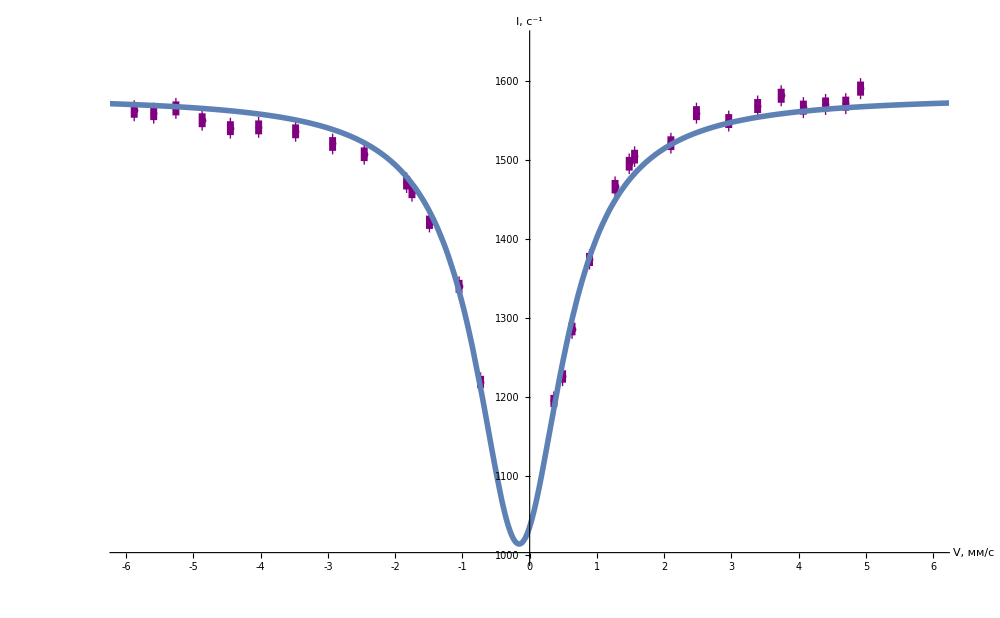

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data4⟦2;;,{2,3,4,4}⟧,
GridLines->{grids@0.25,grids@25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, мм/с","I, c^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,myTicY4},
PlotRange->{{-6,6},{1000,1650}}], 
Plot[fit4@x,{x,-7,7},PlotRange->{{-6,6},{850,1700}}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX4=MapAt[dropLastDot@*ToString,data4,{{2;;,All}}];
forTeX4//TeXForm
```

\left(
\begin{array}{cccc}
 \text{N} & \text{U-} & \text{I-} & \text{} \\
 1 & -5.88 & 1562 & 8.84 \\
 2 & -5.59 & 1559 & 8.83 \\
 3 & -5.26 & 1565 & 8.85 \\
 4 & -4.87 & 1550 & 8.8 \\
 5 & -4.45 & 1540 & 8.77 \\
 6 & -4.03 & 1541 & 8.78 \\
 7 & -3.48 & 1536 & 8.76 \\
 8 & -2.93 & 1520 & 8.72 \\
 9 & -2.46 & 1507 & 8.68 \\
 10 & -1.83 & 1471 & 8.58 \\
 11 & -1.75 & 1460 & 8.54 \\
 12 & -1.49 & 1421 & 8.43 \\
 13 & -1.05 & 1340 & 8.19 \\
 16 & -0.73 & 1219 & 7.81 \\
 17 & 4.92 & 1590 & 8.92 \\
 18 & 4.7 & 1571 & 8.86 \\
 19 & 4.4 & 1570 & 8.86 \\
 20 & 4.07 & 1566 & 8.85 \\
 21 & 3.74 & 1581 & 8.89 \\
 22 & 3.39 & 1568 & 8.85 \\
 23 & 2.96 & 1549 & 8.8 \\
 24 & 2.48 & 1559 & 8.83 \\
 25 & 2.1 & 1521 & 8.72 \\
 26 & 1.56 & 1504 & 8.67 \\
 27 & 1.48 & 1495 & 8.65 \\
 28 & 1.27 & 1466 & 8.56 \\
 29 & 0.89 & 1374 & 8.29 \\
 30 & 0.49 & 1226 & 7.83 \\
 31 & 0.36 & 1195 & 7.73 \\
 32 & 0.63 & 1286 & 8.02 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data2=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/61/tables/nap2.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data2//TableForm
```

N | U- | I- | 
1. | -5.93 | 617.8 | 5.56
2. | -5.59 | 616.5 | 5.55
3. | -5.25 | 621.7 | 5.58
4. | -4.9 | 629.8 | 5.61
5. | -4.47 | 625.9 | 5.59
6. | -4.01 | 616.4 | 5.55
7. | -3.49 | 616.6 | 5.55
8. | -2.98 | 620.5 | 5.57
9. | -2.37 | 622. | 5.58
10. | -1.82 | 617.3 | 5.56
11. | -1.75 | 627.1 | 5.6
12. | -1.48 | 618.9 | 5.56
13. | -1.02 | 616.8 | 5.55
16. | -3.24 | 622.7 | 5.58
17. | -2.62 | 616.3 | 5.55
18. | -3.75 | 615.5 | 5.55
19. | 4.96 | 614.4 | 5.54
20. | 4.68 | 604.5 | 5.5
21. | 4.41 | 608.3 | 5.51
22. | 4.11 | 609.6 | 5.52
23. | 3.75 | 595.1 | 5.45
24. | 3.37 | 594.9 | 5.45
25. | 2.94 | 554. | 5.26
26. | 2.52 | 512.4 | 5.06
27. | 2.03 | 553. | 5.26
28. | 1.55 | 595.2 | 5.46
29. | 1.86 | 600.6 | 5.48
30. | 1.25 | 609.8 | 5.52
31. | 0.87 | 615.4 | 5.55
32. | 2.73 | 531.4 | 5.15
33. | 2.24 | 517.1 | 5.08
34. | 3.16 | 580.1 | 5.39

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit2=Sort@data2⟦2;;,{2,3}⟧;
model =b-a/((x-X)^2/c^2+1);
```

```mathematica
fit2=NonlinearModelFit[forFit2⟦All,{1,2}⟧,{model(*,30<a<250,950<b<990,0.3<c<0.5*)},{{a,560},{b,1580},{c},{X,2.4}},x
,Weights->1/√(forFit2⟦All,2⟧/20)]
fit2@"ParameterTable"
(*Plot[fit["Function"]@x, {x, -5, 5}]*)
```

FittedModel[620.348-114.596/(1+4.20017 (-2.48337+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 114.596 | 5.64592 | 20.2971 | 2.75438×10^-18
b | 620.348 | 1.66715 | 372.101 | 2.85114×10^-53
c | 0.48794 | 0.039011 | 12.5077 | 5.56925×10^-13
X | 2.48337 | 0.0223597 | 111.064 | 1.39727×10^-38

```mathematica
fit2["FitResiduals"]
fit["FitResiduals"]
(*fit2["Properties"]*)
```

{-2.16365,-3.43073,1.8066,9.95051,6.11374,-3.30435,-4.14988,-2.98822,3.1791,1.05904,-3.0097,2.7989,-1.59322,8.25465,0.263166,-1.36714,4.65563,4.96066,-0.551461,23.7897,-5.84631,-11.4802,6.00587,2.32814,-5.25592,-1.0426,1.19104,-10.4394,-1.28753,-5.14055,-10.4593,-1.66586}

{-0.714494,0.307961,625.334,86.3716,-9.58425,0.475591,-8.4358,14.6127,-1.31997,-0.283412,-3.24088,-0.140114,-4.9198,4.09541,-24.8838,-1.70733,0.628373,2.0037,9.05866,2.38084,6.22039,4.02355,-5.2318,-4.11632,-2.58478,10.4549,-0.751103,-14.7076,-4.13278,3.13836,-2.48126,25.6841,-5.03403}

```mathematica
Minimize[620.3477998006515-114.59602380096975/(1+4.200169839125344 (-2.4833656881224675+x)^2),{x}]
```

{505.752,{x→2.48337}}

```mathematica
fit2["CovarianceMatrix"]
```

{{31.8764,1.31746,-0.129609,-0.00977662},{1.31746,2.77939,0.028615,0.000804966},{-0.129609,0.028615,0.00152186,0.0000579079},{-0.00977662,0.000804966,0.0000579079,0.000499956}}

```mathematica
Residue
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY2[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,20}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

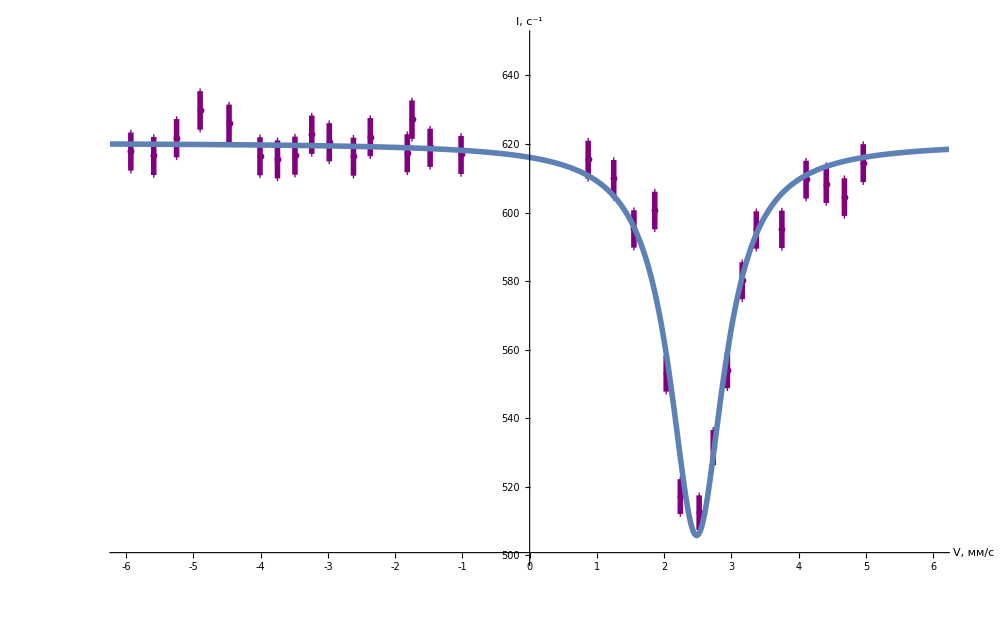

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data2⟦2;;,{2,3,4,4}⟧,
GridLines->{grids@0.25,grids@25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, мм/с","I, c^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,myTicY2},
PlotRange->{{-6,6},{500,650}}], 
Plot[fit2@x,{x,-7,7},PlotRange->{{-6,6},{0,1700}}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX2=MapAt[dropLastDot@*ToString,data2,{{2;;,All}}];
forTeX2//TeXForm
```

\left(
\begin{array}{cccc}
 \text{N} & \text{U-} & \text{I-} & \text{} \\
 1 & -5.93 & 617.8 & 5.56 \\
 2 & -5.59 & 616.5 & 5.55 \\
 3 & -5.25 & 621.7 & 5.58 \\
 4 & -4.9 & 629.8 & 5.61 \\
 5 & -4.47 & 625.9 & 5.59 \\
 6 & -4.01 & 616.4 & 5.55 \\
 7 & -3.49 & 616.6 & 5.55 \\
 8 & -2.98 & 620.5 & 5.57 \\
 9 & -2.37 & 622 & 5.58 \\
 10 & -1.82 & 617.3 & 5.56 \\
 11 & -1.75 & 627.1 & 5.6 \\
 12 & -1.48 & 618.9 & 5.56 \\
 13 & -1.02 & 616.8 & 5.55 \\
 16 & -3.24 & 622.7 & 5.58 \\
 17 & -2.62 & 616.3 & 5.55 \\
 18 & -3.75 & 615.5 & 5.55 \\
 19 & 4.96 & 614.4 & 5.54 \\
 20 & 4.68 & 604.5 & 5.5 \\
 21 & 4.41 & 608.3 & 5.51 \\
 22 & 4.11 & 609.6 & 5.52 \\
 23 & 3.75 & 595.1 & 5.45 \\
 24 & 3.37 & 594.9 & 5.45 \\
 25 & 2.94 & 554 & 5.26 \\
 26 & 2.52 & 512.4 & 5.06 \\
 27 & 2.03 & 553 & 5.26 \\
 28 & 1.55 & 595.2 & 5.46 \\
 29 & 1.86 & 600.6 & 5.48 \\
 30 & 1.25 & 609.8 & 5.52 \\
 31 & 0.87 & 615.4 & 5.55 \\
 32 & 2.73 & 531.4 & 5.15 \\
 33 & 2.24 & 517.1 & 5.08 \\
 34 & 3.16 & 580.1 & 5.39 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data3=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/61/tables/nap3.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data3//TableForm
```

N | U- | I- | 
1. | -5.84 | 163. | 2.85
2. | -5.45 | 165.2 | 2.87
3. | -4.88 | 160.3 | 2.83
4. | -4.24 | 164.4 | 2.87
5. | -3.46 | 166.3 | 2.88
6. | -2.65 | 163.5 | 2.86
7. | -1.75 | 155.8 | 2.79
8. | -1.24 | 163.2 | 2.86
9. | -0.5 | 160.1 | 2.83
10. | -1.82 | 172.6 | 2.94
11. | -2.06 | 162.2 | 2.85
12. | -2.6 | 162.2 | 2.85
13. | -3.24 | 167.4 | 2.89
16. | -3.6 | 163.6 | 2.86
17. | -1.81 | 157.8 | 2.81
18. | -1.74 | 159.2 | 2.82
19. | 4.91 | 157. | 2.8
20. | 4.56 | 160.2 | 2.83
21. | 4.07 | 155.3 | 2.79
22. | 3.57 | 158.6 | 2.82
23. | 2.91 | 134.5 | 2.59
24. | 2.25 | 123.9 | 2.49
25. | 1.5 | 151.3 | 2.75
26. | 1.06 | 155.4 | 2.79
27. | 0.43 | 159.4 | 2.82
29. | 1.77 | 147.7 | 2.72
30. | 2.29 | 125.3 | 2.5
31. | 2.73 | 132.2 | 2.57
32. | 3.11 | 143.3 | 2.68
33. | 1.55 | 152.2 | 2.76
34. | 1.53 | 153.5 | 2.77

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit3=Sort@data3⟦2;;,{2,3}⟧;
model =b-a/((x-X)^2/c^2+1);
```

```mathematica
fit3=NonlinearModelFit[forFit3⟦All,{1,2}⟧,{model(*,30<a<250,950<b<990,0.3<c<0.5*)},{{a,560},{b,1580},{c},{X,2.48}},x
,Weights->1/√(forFit3⟦All,2⟧/20)]
fit3@"ParameterTable"
(*Plot[fit["Function"]@x, {x, -5, 5}]*)
```

FittedModel[163.2-41.7668/(1+2.99562 (-2.45718+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 41.7668 | 2.73603 | 15.2655 | 8.41029×10^-15
b | 163.2 | 0.85859 | 190.079 | 9.33615×10^-44
c | 0.577772 | 0.0643732 | 8.97536 | 1.36899×10^-9
X | 2.45718 | 0.0334003 | 73.5676 | 1.19384×10^-32

```mathematica
fit3["BestFit"]
```

163.2-41.7668/(1+2.99562 (-2.45718+x)^2)

```mathematica
Minimize[163.20043423103604-41.766777311882166/(1+2.995621203356776 (-2.45717770627521+x)^2),{x}]
```

{121.434,{x→2.45718}}

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY3[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,10}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

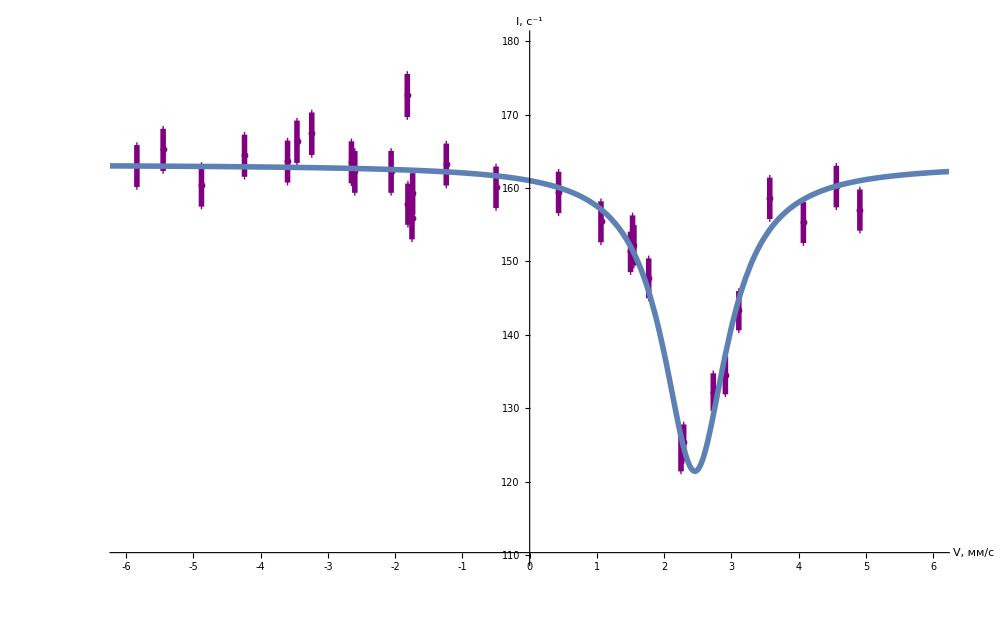

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data3⟦2;;,{2,3,4,4}⟧,
GridLines->{grids@0.25,grids@25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, мм/с","I, c^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,myTicY3},
PlotRange->{{-6,6},{110,180}}], 
Plot[fit3@x,{x,-7,7},PlotRange->{{-6,6},{0,1700}}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX3=MapAt[dropLastDot@*ToString,data3,{{2;;,All}}];
forTeX3//TeXForm
```

\left(
\begin{array}{cccc}
 \text{N} & \text{U-} & \text{I-} & \text{} \\
 1 & -5.84 & 163 & 2.85 \\
 2 & -5.45 & 165.2 & 2.87 \\
 3 & -4.88 & 160.3 & 2.83 \\
 4 & -4.24 & 164.4 & 2.87 \\
 5 & -3.46 & 166.3 & 2.88 \\
 6 & -2.65 & 163.5 & 2.86 \\
 7 & -1.75 & 155.8 & 2.79 \\
 8 & -1.24 & 163.2 & 2.86 \\
 9 & -0.5 & 160.1 & 2.83 \\
 10 & -1.82 & 172.6 & 2.94 \\
 11 & -2.06 & 162.2 & 2.85 \\
 12 & -2.6 & 162.2 & 2.85 \\
 13 & -3.24 & 167.4 & 2.89 \\
 16 & -3.6 & 163.6 & 2.86 \\
 17 & -1.81 & 157.8 & 2.81 \\
 18 & -1.74 & 159.2 & 2.82 \\
 19 & 4.91 & 157 & 2.8 \\
 20 & 4.56 & 160.2 & 2.83 \\
 21 & 4.07 & 155.3 & 2.79 \\
 22 & 3.57 & 158.6 & 2.82 \\
 23 & 2.91 & 134.5 & 2.59 \\
 24 & 2.25 & 123.9 & 2.49 \\
 25 & 1.5 & 151.3 & 2.75 \\
 26 & 1.06 & 155.4 & 2.79 \\
 27 & 0.43 & 159.4 & 2.82 \\
 29 & 1.77 & 147.7 & 2.72 \\
 30 & 2.29 & 125.3 & 2.5 \\
 31 & 2.73 & 132.2 & 2.57 \\
 32 & 3.11 & 143.3 & 2.68 \\
 33 & 1.55 & 152.2 & 2.76 \\
 34 & 1.53 & 153.5 & 2.77 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
data5=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/61/tables/iz.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data5//TableForm
```

N | U, V | I | 
2. | 0.5 | 15.6 | 0.88
3. | 1. | 10.2 | 0.71
4. | 1.5 | 14.6 | 0.85
5. | 2. | 49.6 | 1.57
6. | 2.5 | 84.6 | 2.06
7. | 3. | 84. | 2.05
8. | 3.5 | 123.4 | 2.48
9. | 4. | 152. | 2.76
10. | 4.5 | 187.6 | 3.06
11. | 5. | 183. | 3.02
12. | 5.5 | 169.8 | 2.91
13. | 6. | 100.4 | 2.24
14. | 6.5 | 65.6 | 1.81
15. | 7. | 29.6 | 1.22
16. | 7.5 | 10.8 | 0.73
17. | 8. | 5.4 | 0.52
18. | 8.5 | 4. | 0.45
19. | 9. | 3. | 0.39
20. | 9.5 | 3.4 | 0.41

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit5=Sort@data5⟦2;;,{2,3}⟧;
model =b-a/((x-X)^2/c^2+1);
```

```mathematica
fit5=NonlinearModelFit[forFit5⟦All,{1,2}⟧,{model(*,30<a<250,950<b<990,0.3<c<0.5*)},{{a,560},{b,1580},{c},{X,2.4}},x
,Weights->1/√(forFit5⟦All,2⟧/20)]
fit5@"ParameterTable"
(*Plot[fit["Function"]@x, {x, -5, 5}]*)
```

FittedModel[-23.7507+218.483/(1+0.403285 (-4.56932+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
a | -218.483 | 12.0448 | -18.1393 | 1.29232×10^-11
b | -23.7507 | 7.38793 | -3.2148 | 0.00578587
c | 1.57469 | 0.176942 | 8.89947 | 2.26403×10^-7
X | 4.56932 | 0.0748284 | 61.064 | 2.12943×10^-19

```mathematica
fit2["CovarianceMatrix"]
```

{{31.8764,1.31746,-0.129609,-0.00977662},{1.31746,2.77939,0.028615,0.000804966},{-0.129609,0.028615,0.00152186,0.0000579079},{-0.00977662,0.000804966,0.0000579079,0.000499956}}

```mathematica
ChiSquareDistribution
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY5[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,20}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

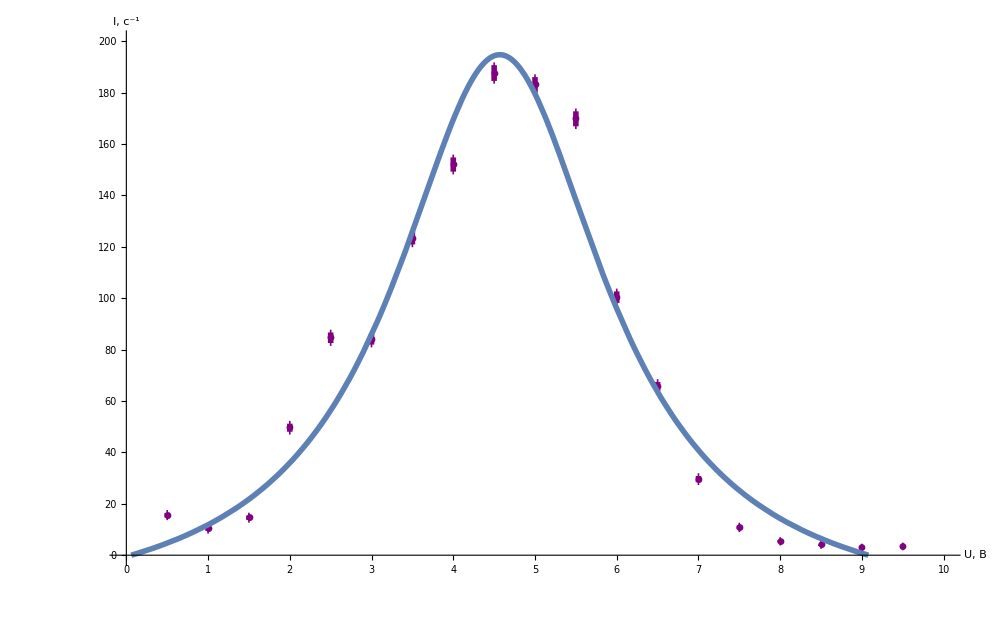

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data5⟦2;;,{2,3,4,4}⟧,
GridLines->{grids@0.25,grids@20},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"U, В","I, c^-1"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.004,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)
(*,horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX,myTicY5},
PlotRange->{{0,10},{0,200}}], 
Plot[fit5@x,{x,-7,10},PlotRange->{{0,10},{0,1700}}, PlotStyle->Thickness@0.004]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX5=MapAt[dropLastDot@*ToString,data5,{{2;;,All}}];
forTeX5//TeXForm
```

\left(
\begin{array}{cccc}
 \text{N} & \text{U, V} & \text{I} & \text{} \\
 2 & 0.5 & 15.6 & 0.88 \\
 3 & 1 & 10.2 & 0.71 \\
 4 & 1.5 & 14.6 & 0.85 \\
 5 & 2 & 49.6 & 1.57 \\
 6 & 2.5 & 84.6 & 2.06 \\
 7 & 3 & 84 & 2.05 \\
 8 & 3.5 & 123.4 & 2.48 \\
 9 & 4 & 152 & 2.76 \\
 10 & 4.5 & 187.6 & 3.06 \\
 11 & 5 & 183 & 3.02 \\
 12 & 5.5 & 169.8 & 2.91 \\
 13 & 6 & 100.4 & 2.24 \\
 14 & 6.5 & 65.6 & 1.81 \\
 15 & 7 & 29.6 & 1.22 \\
 16 & 7.5 & 10.8 & 0.73 \\
 17 & 8 & 5.4 & 0.52 \\
 18 & 8.5 & 4 & 0.45 \\
 19 & 9 & 3 & 0.39 \\
 20 & 9.5 & 3.4 & 0.41 \\
\end{array}
\right)

```mathematica
data6=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/61/tables/fit.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data6//TableForm
```

| a | b | c | d
1. | 103 \pm 6 | 990 \pm 4 | 0,43 \pm 0,04 | 2,41\pm 0,03
2. | 114 \pm 5 | 620 \pm 3 | 0,49 \pm 0,04 | 2,48 \pm 0,02
3. | 41 \pm 3 | 163 \pm 1 | 0,58 \pm 0,06 | 2,46 \pm 0,03
4. | 566\pm 31 | 1580\pm 5 | 0,78\pm 0,05 | -0,156\pm 0,015

```mathematica
forTeX6=MapAt[dropLastDot@*ToString,data6,{{2;;,All}}];
forTeX6//TeXForm
```

\left(
\begin{array}{ccccc}
 \text{} & \text{a} & \text{b} & \text{c} & \text{d} \\
 1 & \text{103 $\backslash \backslash $pm 6} & \text{990 $\backslash \backslash $pm 4} & \text{0,43 $\backslash \backslash $pm 0,04} & \text{2,41$\backslash \backslash
   $pm 0,03} \\
 2 & \text{114 $\backslash \backslash $pm 5} & \text{620 $\backslash \backslash $pm 3} & \text{0,49 $\backslash \backslash $pm 0,04} & \text{2,48 $\backslash \backslash
   $pm 0,02} \\
 3 & \text{41 $\backslash \backslash $pm 3} & \text{163 $\backslash \backslash $pm 1} & \text{0,58 $\backslash \backslash $pm 0,06} & \text{2,46 $\backslash \backslash
   $pm 0,03} \\
 4 & \text{566$\backslash \backslash $pm 31} & \text{1580$\backslash \backslash $pm 5} & \text{0,78$\backslash \backslash $pm 0,05} & \text{-0,156$\backslash \backslash
   $pm 0,015} \\
\end{array}
\right)